## Null frame vielbeins aligned with null radial geodesics

Overview, M.B.Kocic, Version 2, 2017-02-16

A null geodesic is a geodesic, whose tangent vector is a light-like vector everywhere on the geodesic. That is x(λ) is a geodesic and

2ℒ=g_μν(ⅆ x^μ)/ⅆλ(ⅆ x^ν)/ⅆλ=0

for all λ, where λ is an affine parameter along the curve.

In Minkowski spacetime, the nonholonomically constructed null vectors { ℓ^a , 𝓃^a } respectively match the outgoing and ingoing null radial rays.

As an extension of this idea in generic curved spacetimes, { ℓ^a , 𝓃^a } can still be aligned with the tangent vector field of null radial congruence [see Chandrasekhar, The math theory of blackholes].  However, this type of adaption only works for { t , r , θ , ϕ },  { u , r , θ , ϕ }  or { v , r , θ , ϕ } coordinates where the radial behaviors can be well described, with u and v denote the outgoing (retarded) and ingoing (advanced) null coordinate, respectively.

Comments on NP formalism for the case of family of shear-free, null geodesic light rays spaning the null tetrad.

We are working with a null congruence which is basically a family of null curves;  ℓ^a ℓ_a=0 means that ℓ^a is a null vector field, that is, at every point of the manifold, ℓ^a is tangent to a generator of the light cone at this point. There is an infine number of possible null vector fields defining curves on the manifold, but not everyone is a geodesic. In the Newman-Penrose formalism, it is possible, if you already have a null vector field ℓ^a to adapt to it a null tetrad, {ℓ^a,𝓃^a,m^a,(m̄)^a}. Then, one of the directional NP derivatives of the tetrad would be: ℓ^b∇_b ℓ^a=(ϵ+ϵ̄)ℓ^a−κ̄ m^a−κ(m̄)^a, where ϵ and κ are spin coefficients (which are part of the full set of the components of the Ricci rotation coefficients). The Goldberg-Sachs theorem states that if you have a congruence of null geodesics which are shear-free (which this is basically a way of saying that the family of null rays, when evolve in time, they don’t  “distort”), then κ=0 (and other spin coefficient also is zero, but it is not here). So, the null geodesic equation can be put as (ℓ^b∇_b ℓ^a=(ϵ+ϵ̄)ℓ^a, If besides of this, ϵ=0, you have a congruence of null geodesics that have an affine parameter.

References: Section 2.1.3 (pp 10-12) in J.B. Griffiths, J. Podolský, Exact Space-Times in Einstein’s General Relativity, Cambridge University Press, 2009, or Null geodesic congruences in Ezra (Ted) Newman and Roger Penrose (2009) Spin-coefficient formalism. Scholarpedia, 4(6):7445.

## Definitions

We define the most general form of a null frame vielbein with the associated metric. Here we ignore the spherically symmetric radial part { θ , ϕ } for  θ̇=0, ṙ=0.

```mathematica
e=({{Subscript[ℓ, u], Subscript[ℓ, r]}, {Subscript[𝓃, u], Subscript[𝓃, r]}});   η=({{0, -1}, {-1, 0}});
```

```mathematica
g=Transpose[e].η.e;
```

The inverse vielbein (not transposed, thus we have 𝓃⃗ and ℓ⃗ vectors as columns):

```mathematica
ie=Inverse@e;
ie//MatrixForm
```

(𝓃_r/(ℓ_u 𝓃_r-ℓ_r 𝓃_u) | -ℓ_r/(ℓ_u 𝓃_r-ℓ_r 𝓃_u)
-𝓃_u/(ℓ_u 𝓃_r-ℓ_r 𝓃_u) | ℓ_u/(ℓ_u 𝓃_r-ℓ_r 𝓃_u))

Utility function to display the uninstantiated geometry (“uninstantiated” = the components are without particular values):

```mathematica
fullInfo[rules_:{},simplify_:Simplify]:={
Row@{gName/.rules," = ",(conformalFactor Transpose[({{du}, {dr}})].g.({{du}, {dr}})/.rules//simplify//Collect[#,{du,dr}]&)⟦1,1⟧},
Row@{"det ",gName/.rules," = ",Det[conformalFactor g/.rules//simplify]},
Row@{gName/.rules," = ",MatrixForm[conformalFactor g/.rules//simplify]},
Row@{"e = ",MatrixForm[e/.rules//simplify]},
Row@{"det e = ",Det[e/.rules//simplify]},
Row@{"ℓ̃ = ",MatrixForm[{e⟦1⟧/.rules//simplify}]},
Row@{"𝓃̃ = ",MatrixForm[{e⟦2⟧/.rules//simplify}]},
Row@{"e^-1 = ",MatrixForm[ie/.rules//simplify]},
Row@{"ℓ⃗ = ",MatrixForm[ie⟦All,2⟧/.rules//simplify]},
Row@{"𝓃⃗ = ",MatrixForm[ie⟦All,1⟧/.rules//simplify]}
}/.{gName->"g",conformalFactor->1}
```

```mathematica
Row@Riffle[fullInfo[],", "]
```

g = -2 dr^2 ℓ_r 𝓃_r-2 du^2 ℓ_u 𝓃_u-2 dr du (ℓ_u 𝓃_r+ℓ_r 𝓃_u), det g = -ℓ_u^2 𝓃_r^2+2 ℓ_r ℓ_u 𝓃_r 𝓃_u-ℓ_r^2 𝓃_u^2, g = (-2 ℓ_u 𝓃_u | -ℓ_u 𝓃_r-ℓ_r 𝓃_u
-ℓ_u 𝓃_r-ℓ_r 𝓃_u | -2 ℓ_r 𝓃_r), e = (ℓ_u | ℓ_r
𝓃_u | 𝓃_r), det e = ℓ_u 𝓃_r-ℓ_r 𝓃_u, ℓ̃ = (ℓ_u | ℓ_r), 𝓃̃ = (𝓃_u | 𝓃_r), e^-1 = (𝓃_r/(ℓ_u 𝓃_r-ℓ_r 𝓃_u) | ℓ_r/(-ℓ_u 𝓃_r+ℓ_r 𝓃_u)
𝓃_u/(-ℓ_u 𝓃_r+ℓ_r 𝓃_u) | ℓ_u/(ℓ_u 𝓃_r-ℓ_r 𝓃_u)), ℓ⃗ = (ℓ_r/(-ℓ_u 𝓃_r+ℓ_r 𝓃_u)
ℓ_u/(ℓ_u 𝓃_r-ℓ_r 𝓃_u)), 𝓃⃗ = (𝓃_r/(ℓ_u 𝓃_r-ℓ_r 𝓃_u)
𝓃_u/(-ℓ_u 𝓃_r+ℓ_r 𝓃_u))

## Geodesic equation

The geodesics are obtained by the variational method from the following Lagrangian, [see section 7.6 (and also sections 16.4, 18.3 for examples) in d’Inverno, Introducing Einstein’s Relativity, Clarendon Press, 1992]:

2ℒ=(ẋ)^μ g_μν(ẋ)^μ

```mathematica
ℒ=1/2(Transpose[({{u'[λ]}, {r'[λ]}})].g.({{u'[λ]}, {r'[λ]}}))⟦1,1⟧//Simplify;
```

For the radial null gedoesics we have ℒ=0, θ̇=0, ϕ̇=0. In the following we also assume that the frame fields are independent on the u coordinate. Then,

```mathematica
Row@{"ℒ = ",ℒ," = 0"}
D[ℒ,u'[λ]]==const   (* from D[D[ℒ,u'],λ] - D[ℒ,u] == 0 *)
```

ℒ = -(ℓ_r r'[λ]+ℓ_u u'[λ]) (𝓃_r r'[λ]+𝓃_u u'[λ]) = 0

-𝓃_u (ℓ_r r'[λ]+ℓ_u u'[λ])-ℓ_u (𝓃_r r'[λ]+𝓃_u u'[λ])==const

This gives the “solution” [actually, the vector fields which will yield the solution]:

```mathematica
vec$ℓ={u'[λ],r'[λ]}/.Solve[{D[ℒ,u'[λ]]==-1,ℒ==0},{u'[λ],r'[λ]}]⟦1⟧//Simplify
```

{-ℓ_r/(ℓ_u^2 𝓃_r-ℓ_r ℓ_u 𝓃_u),1/(ℓ_u 𝓃_r-ℓ_r 𝓃_u)}

```mathematica
vec$𝓃={u'[λ],r'[λ]}//.Solve[{D[ℒ,u'[λ]]==-1,ℒ==0},{u'[λ],r'[λ]}]⟦2⟧//Simplify
```

{𝓃_r/(ℓ_u 𝓃_r 𝓃_u-ℓ_r 𝓃_u^2),1/(-ℓ_u 𝓃_r+ℓ_r 𝓃_u)}

Now, scaling of the vector fields by 𝓃_u (or ℓ_u )does not influence the stream flow. [That is since the vector fields are autonomous, i.e., they do not depend on λ (just parameterized by λ) so  the scaling just reparameterizes λ.]  Morever, the scaling makes the stream flow regular (in the case if  𝓃_u or ℓ_u are zero). As a consequence, we can take the vector fields ℓ⃗ and 𝓃⃗  as generators of the radial null geodesics. Of course, this is the expected fact that the null cone field will generate the null geodesics.

```mathematica
{Subscript[ℓ, u],Subscript[ℓ, u]}vec$ℓ//Simplify
Row@{"Equal to ℓ⃗? >>> ",(%==ie⟦All,2⟧//Simplify )}
```

{ℓ_r/(-ℓ_u 𝓃_r+ℓ_r 𝓃_u),ℓ_u/(ℓ_u 𝓃_r-ℓ_r 𝓃_u)}

Equal to ℓ⃗? >>> True

```mathematica
{Subscript[𝓃, u],Subscript[𝓃, u]}vec$𝓃//Simplify
Row@{"Equal to 𝓃⃗? >>> ",(%==ie⟦All,1⟧//Simplify )}
```

{𝓃_r/(ℓ_u 𝓃_r-ℓ_r 𝓃_u),𝓃_u/(-ℓ_u 𝓃_r+ℓ_r 𝓃_u)}

Equal to 𝓃⃗? >>> True

## Examples

#### Null tetrad for Schwarzschild metric in Eddington-Finkestein coordinates

Ingoing chart (v,r)

The ingoing Eddington–Finkelstein coordinates are obtained by replacing the coordinate t with the new coordinate v = t + r^*. The metric in these coordinates can be written:

d s^2==-(1-r_s/r)d v^2+2 dv dr +r^2 dΩ^2.

One needs to remember, though, that v (usually called an advanced time) is a lightlike coordinate (neither spatial nor temporal). For a second coordinate, we can choose the familiar coordinate r. The congruence of ingoing radial null geodesies is given by v=constant, i.e., coordinate lines of constant v, representing ingoing radial null rays, are plotted on a 45-degree slant, just as they would be in flat spacetime.

```mathematica
ingoingNullCongruences[rH_,Λ_,Q_]:=Block[
{F,v$ℓ,v$𝓃,corr,horizons},
F=1-rH/r-Λ/3 r^2+Q/r^2+(Λ rH^3)/(3 r);
corr=0; (* 0 = v, 1 = t' on y-axis *)
v$ℓ={1-corr*(F/2),F/2}//RotateLeft;
v$𝓃={0-corr*(-1),-1}//RotateLeft;
horizons=NSolve[F==0&&r>0,r];
horizons=If[horizons=!={},r/.horizons,{}];
{
Plot[
F,
{r,0,4},
PlotRange->{-2,2},
PlotTheme->"Scientific",
PlotLabel->Column@{
Row@{"r_H = ",rH,", Λ = ",Λ,", Q = ",Q},
Row@{"F(r) = ",F//InputForm},
Row@{"r_H ∈ ",horizons}
},
Axes->True,
AspectRatio->1,GridLines->Automatic,
ImageSize->Scaled[0.3]
],
StreamPlot[
{v$𝓃,v$ℓ},
{r,0.001,10},
{v,-20,20},
PlotRange->{{0,10},{-10,10}},
Evaluate[Sequence@@If[True,{PlotTheme->"Scientific"},
{Axes->{False,False},FrameTicks->None,Frame->None}
]],
StreamPoints->{
If[Not[rH==0∧Λ<0],Table[{0.1,v},{v,-If[rH==0&&Λ==0,8,16],16,2}],{}]~Join~
If[rH!=0∧Λ≥0,Table[{r,-10},{r,3,4.99,2}],{}]~Join~
If[rH≠0&&Λ>0,Table[{r,0},{r,0.8,2,0.2}],{}]~Join~
Table[{10,v},{v,-16,10,2}]~Join~
If[rH≠0&&Λ==0,Table[{r,10},{r,-16,8,1}],{}],
30,30
},
StreamStyle->{{Opacity[0.5],Blue},{Opacity[0.5],Red}},
ImageSize->Scaled[0.4],
PlotLegends->Placed[{
Style["𝓃, ingoing, v = const",14,Blue],
Style["ℓ, outgoing, u = const",14,Red]
},Above],
Epilog->{Black,Dashed,Line[{{#,-10},{#,10}}]&/@horizons}
]
}
]
```

g = 2 dr dv-dv^2 F, det g = -1, g = (-F | 1
1 | 0), e = (F/2 | -1
1 | 0), det e = 1, ℓ̃ = (F/2 | -1), 𝓃̃ = (1 | 0), e^-1 = (0 | 1
-1 | F/2), ℓ⃗ = (1
F/2), 𝓃⃗ = (0
-1)

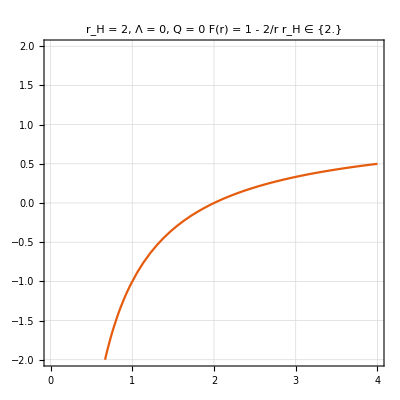
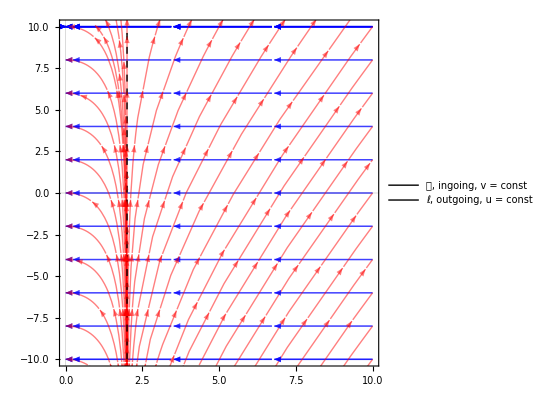

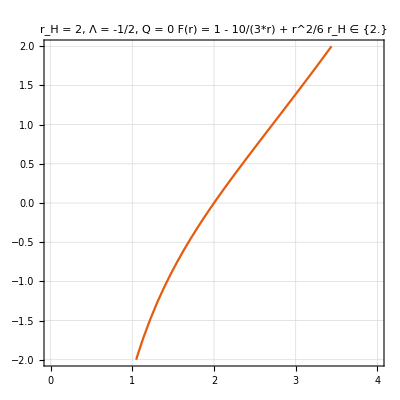
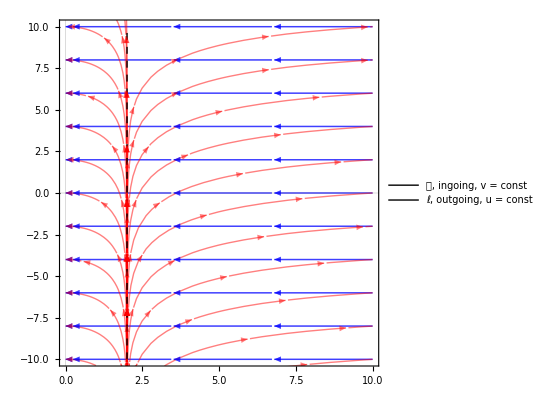

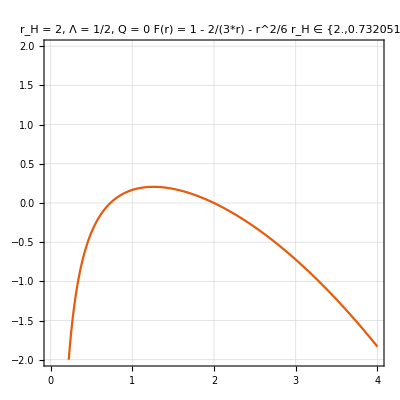
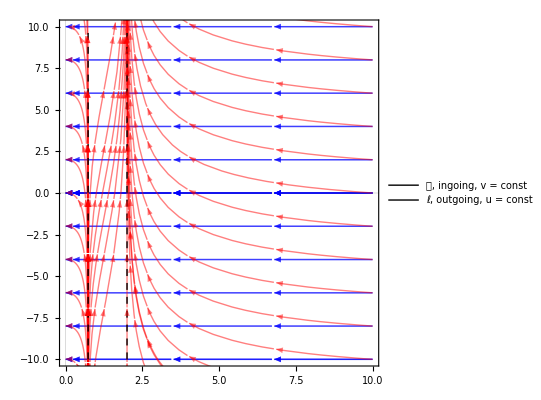

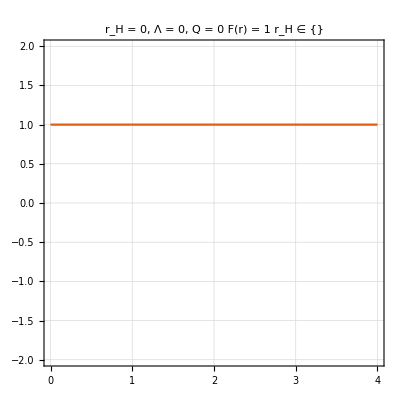
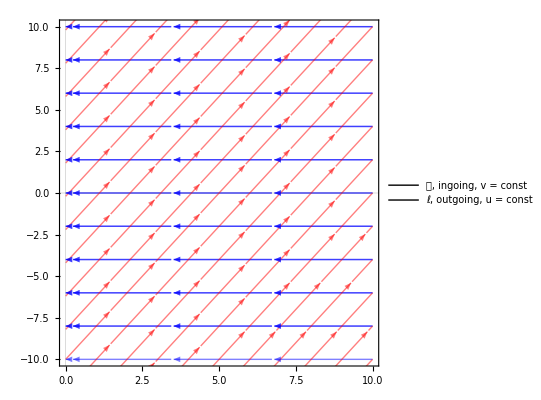

```mathematica
CellPrint[Cell["","PageBreak"]]
Row@Riffle[fullInfo[{Subscript[𝓃, r]->0,Subscript[𝓃, u]->1,Subscript[ℓ, r]->-1,Subscript[ℓ, u]->F/2},#/.{dr->dr,du->dv}&],", "]
Row@Riffle[ingoingNullCongruences[(*rH*) 2, (*Λ*) 0, (*Q*) 0 ],", "]
Row@Riffle[ingoingNullCongruences[(*rH*) 2, (*Λ*) -1/2, (*Q*) 0 ],", "]
Row@Riffle[ingoingNullCongruences[(*rH*) 2, (*Λ*) 1/2, (*Q*) 0 ],", "]
Row@Riffle[ingoingNullCongruences[(*rH*) 0, (*Λ*) 0, (*Q*) 0 ],", "]
Row@Riffle[ingoingNullCongruences[(*rH*) 0, (*Λ*) -1/2, (*Q*) 0 ],", "]
Row@Riffle[ingoingNullCongruences[(*rH*) 0, (*Λ*) 1/2, (*Q*) 0 ],", "]
```

Outgoing chart (u,r)

Another type of the Eddington-Finkelstein coordinates are (u,r), where u = t - r^* is the retarded time. The congruence of outgoing radial null geodesies is given by u=constant.

The outgoing Eddington–Finkelstein coordinates are obtained by replacing t with the null coordinate u = t − r^*. The metric is then given by,

d s^2==-(1-r_s/r)du^2-2 du dr+ +r^2 dΩ^2.

```mathematica
outgoingNullCongruences[rH_,Λ_,Q_]:=Block[
{F,v$ℓ,v$𝓃,corr,horizons},
F=1-rH/r-Λ/3 r^2+Q/r^2+(Λ rH^3)/(3 r);
corr=0; (* 0 = u, 1 = t' on y-axis *)
v$ℓ={1+corr*(-F/2),-F/2}//RotateLeft;
v$𝓃={0+corr*(1),1}//RotateLeft;
horizons=NSolve[F==0&&r>0,r];
horizons=If[horizons=!={},r/.horizons,{}];
{
Plot[
F,
{r,0,4},
PlotRange->{-2,2},
PlotTheme->"Scientific",
PlotLabel->Column@{
Row@{"r_H = ",rH,", Λ = ",Λ,", Q = ",Q},
Row@{"F(r) = ",F//InputForm},
Row@{"r_H ∈ ",horizons}
},
Axes->True,AspectRatio->1,GridLines->Automatic,
ImageSize->Scaled[0.3]
],
StreamPlot[
{v$𝓃,v$ℓ},
{r,0.001,10},
{u,-20,20},
PlotRange->{{0,10},{-10,10}},
Evaluate[Sequence@@If[True,{PlotTheme->"Scientific"},
{Axes->{False,False},FrameTicks->None,Frame->None}
]],
StreamPoints->{
If[Not[rH==0∧Λ<0],Table[{0.1,v},{v,-16,If[rH==0&&Λ==0,8,16],2}],{}]~Join~
If[rH≠0∧Λ≥0,Table[{r,10},{r,3,4.99,2}],{}]~Join~
If[rH≠0&&Λ>0,Table[{r,0},{r,0.8,2,0.2}],{}]~Join~
Table[{10,v},{v,-10,16,2}]~Join~
If[rH≠0&&Λ==0,Table[{r,-10},{r,-16,8,1}],{}],
30,30
},
StreamStyle->{{Opacity[0.5],Red},{Opacity[0.5],Blue}},
ImageSize->Scaled[0.4],
PlotLegends->Placed[{
Style["𝓃, outgoing, u = const",14,Red],
Style["ℓ, ingoing, v = const",14,Blue]
},Above],
Epilog->{Black,Dashed,Line[{{#,-10},{#,10}}]&/@horizons}
]
}
]
```

g = -2 dr du-du^2 F, det g = -1, g = (-F | -1
-1 | 0), e = (F/2 | 1
1 | 0), det e = -1, ℓ̃ = (F/2 | 1), 𝓃̃ = (1 | 0), e^-1 = (0 | 1
1 | -F/2), ℓ⃗ = (1
-F/2), 𝓃⃗ = (0
1)

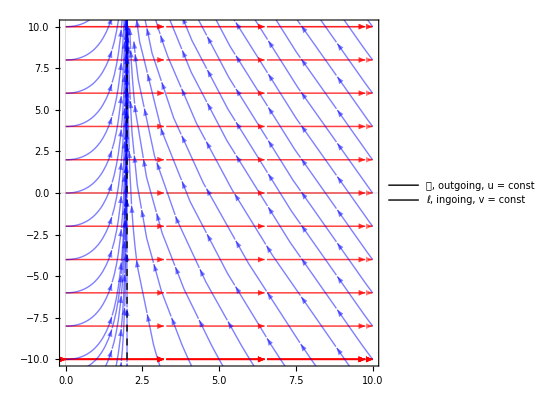
-Graphics-, -Graphics-

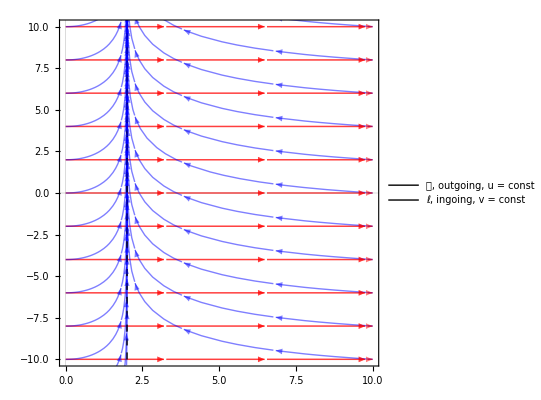
-Graphics-, -Graphics-

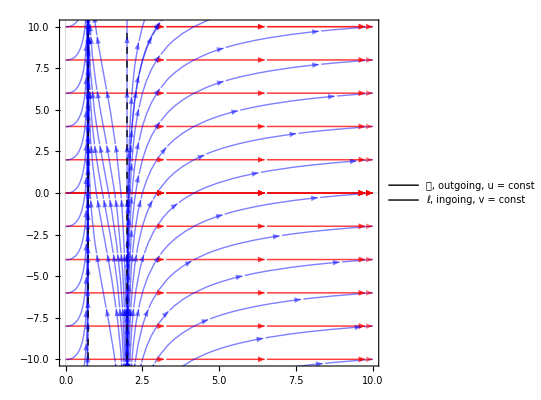
-Graphics-, -Graphics-

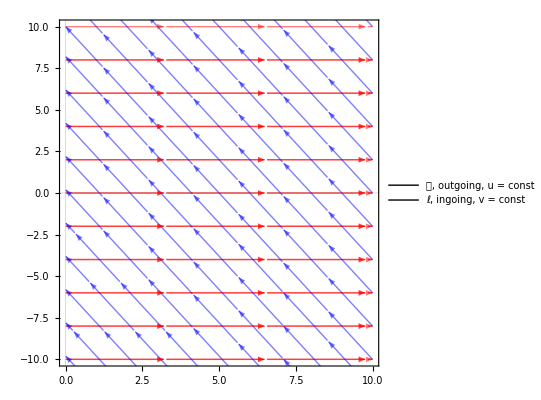
-Graphics-, -Graphics-

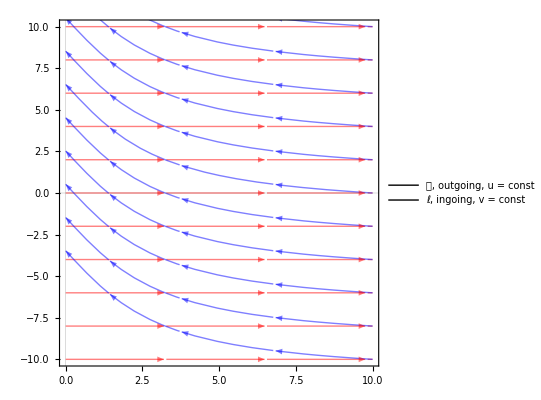
-Graphics-, -Graphics-

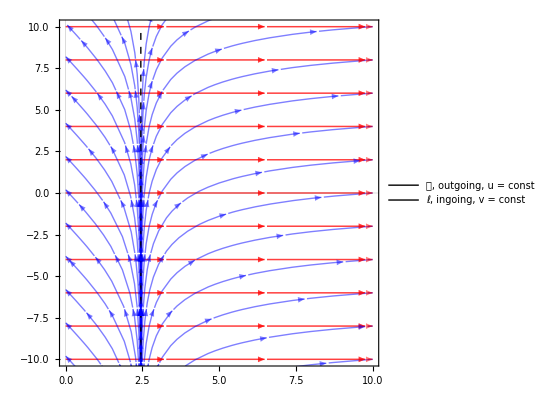
-Graphics-, -Graphics-

```mathematica
CellPrint[Cell["","PageBreak"]]
Row@Riffle[fullInfo[{Subscript[𝓃, r]->0,Subscript[𝓃, u]->1,Subscript[ℓ, r]->1,Subscript[ℓ, u]->F/2}]/.{dr->dr,du->du},", "]
Row@Riffle[outgoingNullCongruences[(*rH*) 2, (*Λ*) 0, (*Q*) 0 ],", "]
Row@Riffle[outgoingNullCongruences[(*rH*) 2, (*Λ*) -1/2, (*Q*) 0 ],", "]
Row@Riffle[outgoingNullCongruences[(*rH*) 2, (*Λ*) 1/2, (*Q*) 0 ],", "]
Row@Riffle[outgoingNullCongruences[(*rH*) 0, (*Λ*) 0, (*Q*) 0 ],", "]
Row@Riffle[outgoingNullCongruences[(*rH*) 0, (*Λ*) -1/2, (*Q*) 0 ],", "]
Row@Riffle[outgoingNullCongruences[(*rH*) 0, (*Λ*) 1/2, (*Q*) 0 ],", "]
```

#### Bim BH metric g in the ingoing chart (v,r)

```mathematica
fullInfo@{Subscript[𝓃, r]->0,Subscript[𝓃, u]->-(-ⅇ^(q/2)),Subscript[ℓ, r]->-(1),Subscript[ℓ, u]->1/2 ⅇ^(q/2) F}/.{dr->dr,du->dv}//Simplify
```

{g = 2 dr dv ⅇ^(q/2)-dv^2 ⅇ^q F,det g = -ⅇ^q,g = (-ⅇ^q F | ⅇ^(q/2)
ⅇ^(q/2) | 0),e = (1/2 ⅇ^(q/2) F | -1
ⅇ^(q/2) | 0),det e = ⅇ^(q/2),ℓ̃ = (1/2 ⅇ^(q/2) F | -1),𝓃̃ = (ⅇ^(q/2) | 0),e^-1 = (0 | ⅇ^(-q/2)
-1 | F/2),ℓ⃗ = (ⅇ^(-q/2)
F/2),𝓃⃗ = (0
-1)}

```mathematica
%/.{q->0}//Simplify
```

{g = dv (2 dr-dv F),det g = -1,g = (-F | 1
1 | 0),e = (F/2 | -1
1 | 0),det e = 1,ℓ̃ = (F/2 | -1),𝓃̃ = (1 | 0),e^-1 = (0 | 1
-1 | F/2),ℓ⃗ = (1
F/2),𝓃⃗ = (0
-1)}

#### Bim BH metric f in the ingoing chart (v,r)

```mathematica
fullInfo@{gName->"f",Subscript[𝓃, r]->ⅇ^(q/2) Σ τ ⅇ^(-q/2)(Σ-τ)/(F Σ τ),Subscript[𝓃, u]->-ⅇ^(q/2) Σ τ(-1/Σ),Subscript[ℓ, r]->-ⅇ^(q/2) Σ τ(ⅇ^(-q/2) (Σ+τ)/(2 Σ τ)),Subscript[ℓ, u]->ⅇ^(q/2) Σ τ 1/(2 Σ)F}/.{dr->dr,du->dv}//Simplify
```

{f = 2 dr dv ⅇ^(q/2) τ^2-dv^2 ⅇ^q F τ^2+(dr^2 (Σ^2-τ^2))/F,det f = -ⅇ^q Σ^2 τ^2,f = (-ⅇ^q F τ^2 | ⅇ^(q/2) τ^2
ⅇ^(q/2) τ^2 | ((Σ-τ) (Σ+τ))/F),e = (1/2 ⅇ^(q/2) F τ | 1/2 (-Σ-τ)
ⅇ^(q/2) τ | (Σ-τ)/F),det e = ⅇ^(q/2) Σ τ,ℓ̃ = (1/2 ⅇ^(q/2) F τ | 1/2 (-Σ-τ)),𝓃̃ = (ⅇ^(q/2) τ | (Σ-τ)/F),e^-1 = ((ⅇ^(-q/2) (Σ-τ))/(F Σ τ) | (ⅇ^(-q/2) (Σ+τ))/(2 Σ τ)
-1/Σ | F/(2 Σ)),ℓ⃗ = ((ⅇ^(-q/2) (Σ+τ))/(2 Σ τ)
F/(2 Σ)),𝓃⃗ = ((ⅇ^(-q/2) (Σ-τ))/(F Σ τ)
-1/Σ)}

```mathematica
%/.{q->0,Σ->1,τ->1,R->1}//Simplify
```

{f = dv (2 dr-dv F),det f = -1,f = (-F | 1
1 | 0),e = (F/2 | -1
1 | 0),det e = 1,ℓ̃ = (F/2 | -1),𝓃̃ = (1 | 0),e^-1 = (0 | 1
-1 | F/2),ℓ⃗ = (1
F/2),𝓃⃗ = (0
-1)}

#### Bim BH metric g in the outgoing chart (u,r)

```mathematica
fullInfo@{Subscript[𝓃, r]->0,Subscript[𝓃, u]->-(-ⅇ^(q/2)),Subscript[ℓ, r]->+(1),Subscript[ℓ, u]->1/2 ⅇ^(q/2) F}/.{dr->dr,du->du}//Simplify
```

{g = -2 dr du ⅇ^(q/2)-du^2 ⅇ^q F,det g = -ⅇ^q,g = (-ⅇ^q F | -ⅇ^(q/2)
-ⅇ^(q/2) | 0),e = (1/2 ⅇ^(q/2) F | 1
ⅇ^(q/2) | 0),det e = -ⅇ^(q/2),ℓ̃ = (1/2 ⅇ^(q/2) F | 1),𝓃̃ = (ⅇ^(q/2) | 0),e^-1 = (0 | ⅇ^(-q/2)
1 | -F/2),ℓ⃗ = (ⅇ^(-q/2)
-F/2),𝓃⃗ = (0
1)}

```mathematica
%/.{q->0}//Simplify
```

{g = -du (2 dr+du F),det g = -1,g = (-F | -1
-1 | 0),e = (F/2 | 1
1 | 0),det e = -1,ℓ̃ = (F/2 | 1),𝓃̃ = (1 | 0),e^-1 = (0 | 1
1 | -F/2),ℓ⃗ = (1
-F/2),𝓃⃗ = (0
1)}

#### Bim BH metric f in the outgoing chart (u,r)

```mathematica
fullInfo@{gName->"f",Subscript[𝓃, r]->-ⅇ^(q/2) Σ τ ⅇ^(-q/2)(Σ-τ)/(F Σ τ),Subscript[𝓃, u]->-ⅇ^(q/2) Σ τ(-1/Σ),Subscript[ℓ, r]->ⅇ^(q/2) Σ τ(ⅇ^(-q/2) (Σ+τ)/(2 Σ τ)),Subscript[ℓ, u]->ⅇ^(q/2) Σ τ 1/(2 Σ)F}/.{dr->dr,du->du}//Simplify
```

{f = -2 dr du ⅇ^(q/2) τ^2-du^2 ⅇ^q F τ^2+(dr^2 (Σ^2-τ^2))/F,det f = -ⅇ^q Σ^2 τ^2,f = (-ⅇ^q F τ^2 | -ⅇ^(q/2) τ^2
-ⅇ^(q/2) τ^2 | ((Σ-τ) (Σ+τ))/F),e = (1/2 ⅇ^(q/2) F τ | (Σ+τ)/2
ⅇ^(q/2) τ | (-Σ+τ)/F),det e = -ⅇ^(q/2) Σ τ,ℓ̃ = (1/2 ⅇ^(q/2) F τ | (Σ+τ)/2),𝓃̃ = (ⅇ^(q/2) τ | (-Σ+τ)/F),e^-1 = ((ⅇ^(-q/2) (Σ-τ))/(F Σ τ) | (ⅇ^(-q/2) (Σ+τ))/(2 Σ τ)
1/Σ | -F/(2 Σ)),ℓ⃗ = ((ⅇ^(-q/2) (Σ+τ))/(2 Σ τ)
-F/(2 Σ)),𝓃⃗ = ((ⅇ^(-q/2) (Σ-τ))/(F Σ τ)
1/Σ)}

```mathematica
%/.{q->0,Σ->1,τ->1,R->1}//Simplify
```

{f = -du (2 dr+du F),det f = -1,f = (-F | -1
-1 | 0),e = (F/2 | 1
1 | 0),det e = -1,ℓ̃ = (F/2 | 1),𝓃̃ = (1 | 0),e^-1 = (0 | 1
1 | -F/2),ℓ⃗ = (1
-F/2),𝓃⃗ = (0
1)}

## Part 2: pp-Wave

The Schwarzschild  metric in the chart { u, r, θ, ϕ } with F=F(r) has the similar structure as the pp-wave metric in { u, v, x, y } with F=F(u,x,y) (especially if we put x, y on a cylinder).

Let us introduce the light-cone coordinate system (u, v, r⃗), where u=t-z, v=t+z and r⃗=(x,y).  Here, v is an advanced while u is a retarted coordinate.

u=t-z,  v=t+z  ⟹  t=(u+v)/2,  z=(v-u)/2,

u-axis:  v=const=0, u=p∈ℝ  ⟹  t=p/2,  z=-p/2,

v-axis:   u=const=0, v=p∈ℝ  ⟹   t=p/2,  z=p/2.

In these coordinates, a generic pp-wave spacetime has the following metric:

d s^2=-du dv +F(u,r)d u^2+dr^2.

This geometry enjoys the null Killing vector ∂_v .

The following profile of a sandwich wave solves the MGr EoM (see X.O. Camanho, G.L. Gómez, R. Rahman, Causality Constraints on Massive Gravity, https://arxiv.org/abs/1610.02033):

-Graphics-

The sandwich wave moves at the speed of light in the v-direction (i.e., in the z-direction since: v=t+z). Its amplitude and width are deffined by a and λ respectively.

Remark. We choose the amplitude a such that the integral of ∫_-λ^λ A(u)du is λ. This amounts to the choice a≈0.933. We also choose the width λ to be larger than the resolution length of the effective field theory: λ>1/Λ. The latter choice is possible for a very large energy of the source: E≫Λ. This situation is completely acceptable and does not at all invalidate the effective field theory descripton. (The situation is analogous to having a macroscopic (super-Planckian) black hole in General Relativity.)

```mathematica
Fg[u_,r_,a_,λ_,m_]:=A[u,a,λ]Piecewise[{{BesselK[0,m Abs@r], m Abs@r≥10^-30}, {70, True}}]
```

```mathematica
A[u_,a_,λ_]:=Piecewise[{{a Exp[-(λ^2 u^2)/((u^2-λ^2)^2)], -λ<u<λ}, {0, True}}]
```

```mathematica
If[False,Manipulate[
SliceDensityPlot3D[
Fg[(*u*)t-z,(*r*)(x^2+y^2)^(1/2),0.93,1,1],
Thread[(-z)==Subdivide[-3,3,10]],
{z,-3,3},{x,-2,2},{y,-2,2},AxesLabel->{z,x,y},BoxRatios->{2,1,1},
BoundaryStyle->None,BaseStyle->{FontFamily->"Cambria",12},
ColorFunction->(Directive[Blue,Opacity@Rescale[#,{0.1,1},{0.15,0.8}]]&)],
{{t,0},-3,3},SaveDefinitions->True
]]
```

{g = -du dv+du^2 F,det g = -1/4,g = (F | -1/2
-1/2 | 0),e = (1/(√2) | 0
-F/(√2) | 1/(√2)),det e = 1/2,ℓ̃ = (1/(√2) | 0),𝓃̃ = (-F/(√2) | 1/(√2)),e^-1 = (√2 | 0
√2 F | √2),ℓ⃗ = (0
√2),𝓃⃗ = (√2
√2 F)}

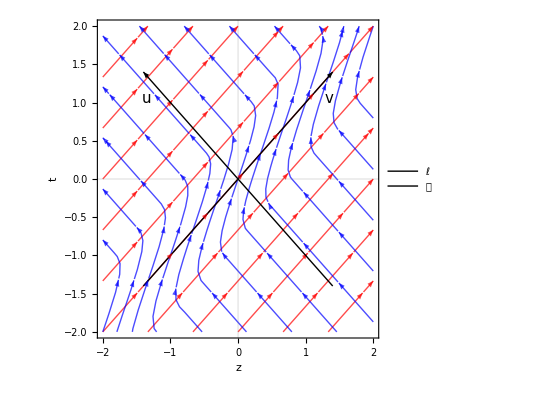

```mathematica
CellPrint[Cell["","PageBreak"]]
fullInfo@{Subscript[𝓃, r]->2^(-1/2),Subscript[𝓃, u]->-F/2^(1/2),Subscript[ℓ, r]->0,Subscript[ℓ, u]->2^(-1/2)}/.{du->du,dr->dv}
Block[
{F,v$ℓ,v$𝓃,plot,r=0.1,range=1},
F=Fg[N@u,N@r,0.93,1.,1.];
(* t = ( v - u ) / 2, z = ( u + v ) / 2 *)
v$ℓ[z_,t_]={#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@({0,2^(1/2)}/.{u->t-z,v->t+z});
v$𝓃[z_,t_]={#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@({2^(1/2),2^(1/2)F}/.{u->t-z,v->t+z});
plot=Show[
StreamPlot[v$ℓ[z,t],
{z,-2range,2range},{t,-2range,2range},FrameLabel->{z,t},
PlotTheme->"Scientific",
PlotRange->{{-2,2},{-2,2}}range,
StreamStyle->{Opacity[0.7],Red},
StreamPoints->{Table[{-u,u},{u,-2range,2range,range/3}],5,5},
PlotLegends->Placed[{Style[ℓ,14,Red]},Right],
WorkingPrecision->30,BaseStyle->{FontFamily->"Cambria",12}
],
StreamPlot[v$𝓃[z,t],
{z,-2range,2range},{t,-2range,2range},FrameLabel->{z,t},
PlotTheme->"Scientific",
StreamStyle->{Opacity[0.7],Blue},
StreamPoints->{Table[{v,v},{v,-2range,2range,range/3}],5,5},
PlotLegends->Placed[{Style[𝓃,14,Blue]},Right],
WorkingPrecision->30,BaseStyle->{FontFamily->"Cambria",12}
],
Graphics[{Black,
Arrow[1.4{{-1,-1},{1,1}}],Text[Style[v,15],1.5{0.9,0.7}],
Arrow[1.4{{1,-1},{-1,1}}],Text[Style[u,15],1.5{-0.9,0.7}]
}],
ImageSize->Scaled[0.6]
]
]
```

## de Sitter & anti de Sitter Penrose-Carter diagrams

The Penrose-Carter diagrams for the de Sitter spacetime (left below) and the anti-de Sitter spacetime (right below). The same copies of the basic portion are attached at the dashed lines. Thick curves correspond to the (A)dS infinity.  Observe that the AdS infinity is timelike.

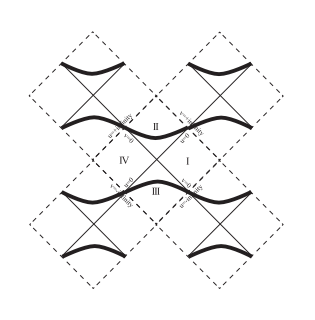
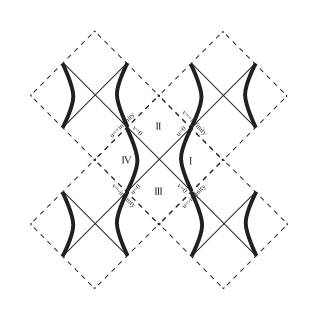

Each diagram below is obtained from one maximally extended portion in the corresponding upper diagram. The double lines in the lower left diagram are identified.  The isolated points i^+ and i^- in the lower right diagram are future and past timelike infinities, respectively. (See: G.W. Gibbons, S.W. Hawking, Cosmological event horizons, thermodynamics, and particle creation, Physical Review D. 15 (1977) 2738–2751.)

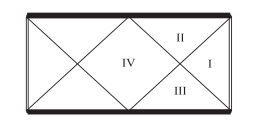
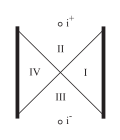

## References

J.B. Griffiths and J. Podolský, Exact Space-Times in Einstein’s General Relativity (CUP, 2009).

#### Schwarzschild

-Graphics-

-Graphics-

-Graphics-

#### Schwarzschild when m<0

-Graphics-

#### de Sitter

-Graphics-

-Graphics-

#### Anti de Sitter

-Graphics-

-Graphics-

-Graphics-

#### Schwarzschild - de Sitter

-Graphics-
-Graphics-

-Graphics-

-Graphics-

#### Schwarzschild - Anti de Sitter

-Graphics-

-Graphics-

#### pp-wave

-Graphics-

-Graphics-